```mathematica
curr1=Import[NotebookDirectory[]<>"newdata.csv"];
curr2=Import[NotebookDirectory[]<>"newdata.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data = {curr1[[All,3]],curr2[[All,4]]}//Transpose;
labels = curr1[[All,1]];
ListPlot[data->labels,Joined->True,LabelingFunction->Automatic,PlotRange->All, PlotMarkers->{●}, PlotLabel->"BTC", AxesLabel->{"USD","GOLD"}]
```

-Graphics-

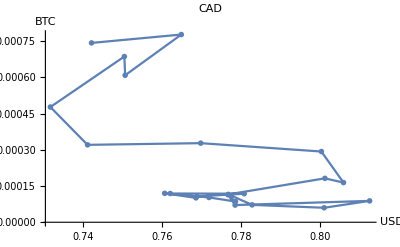

```mathematica
curr1=Import[NotebookDirectory[]<>"newdata.csv"];
curr2=Import[NotebookDirectory[]<>"newdata.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data = {curr1[[All,7]],curr2[[All,8]]}//Transpose;
labels = curr1[[All,1]];
ListPlot[data->data,Joined->True,LabelingFunction->Automatic,PlotRange->All, PlotMarkers->{●}, PlotLabel->"CAD", AxesLabel->{"USD","BTC"}]
```

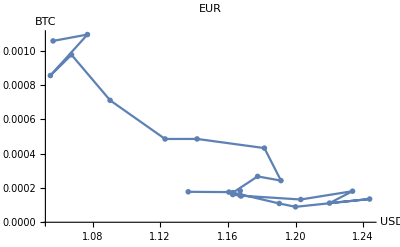

```mathematica
curr1=Import[NotebookDirectory[]<>"newdata.csv"];
curr2=Import[NotebookDirectory[]<>"newdata.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data = {curr1[[All,11]],curr2[[All,12]]}//Transpose;
labels = curr1[[All,1]];
ListPlot[data->data,Joined->True,LabelingFunction->Automatic,PlotRange->All, PlotMarkers->{●}, PlotLabel->"EUR", AxesLabel->{"USD","BTC"}]
```

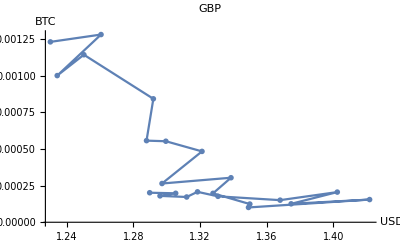

```mathematica
curr1=Import[NotebookDirectory[]<>"newdata.csv"];
curr2=Import[NotebookDirectory[]<>"newdata.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data = {curr1[[All,9]],curr2[[All,10]]}//Transpose;
labels = curr1[[All,1]];
ListPlot[data->data,Joined->True,LabelingFunction->Automatic,PlotRange->All, PlotMarkers->{●}, PlotLabel->"GBP", AxesLabel->{"USD","BTC"}]
```

```mathematica
curr1=Import[NotebookDirectory[]<>"newdata.csv"];
curr2=Import[NotebookDirectory[]<>"newdata.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data = {curr1[[All,13]],curr2[[All,14]]}//Transpose;
labels = curr1[[All,1]];
ListPlot[data->labels,Joined->True,LabelingFunction->Automatic,PlotRange->All, PlotMarkers->{●}, PlotLabel->"ETH", AxesLabel->{"USD","BTC"},ImageSize->400]
```

-Graphics-

```mathematica
curr1=Import[NotebookDirectory[]<>"newdata.csv"];
curr2=Import[NotebookDirectory[]<>"newdata.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data = {curr1[[All,15]],curr2[[All,16]]}//Transpose;
labels = curr1[[All,1]];
ListPlot[data->labels,Joined->True,LabelingFunction->Automatic,PlotRange->All, PlotMarkers->{●}, PlotLabel->"XRP", AxesLabel->{"USD","BTC"},ImageSize->400]
```

-Graphics-

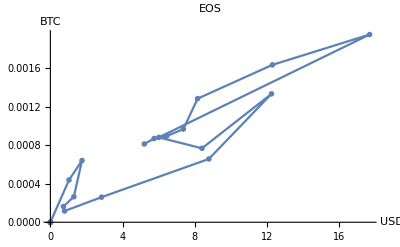

```mathematica
curr1=Import[NotebookDirectory[]<>"newdata.csv"];
curr2=Import[NotebookDirectory[]<>"newdata.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data = {curr1[[All,17]],curr2[[All,18]]}//Transpose;
labels = curr1[[All,1]];
ListPlot[data->data,Joined->True,LabelingFunction->Automatic,PlotRange->All, PlotMarkers->{●}, PlotLabel->"EOS", AxesLabel->{"USD","BTC"}]
```

```mathematica
curr1=Import[NotebookDirectory[]<>"newdata.csv"];
curr2=Import[NotebookDirectory[]<>"newdata.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data = {curr1[[All,21]],curr2[[All,22]]}//Transpose;
labels = curr1[[All,1]];
ListPlot[data->labels,Joined->True,LabelingFunction->Automatic,PlotRange->All, PlotMarkers->{●}, PlotLabel->"TETHER", AxesLabel->{"USD","BTC"},
 ImageSize->800]
```

-Graphics-

```mathematica
curr1=Import[NotebookDirectory[]<>"newdata.csv"];
curr2=Import[NotebookDirectory[]<>"newdata.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data = {curr1[[All,23]],curr2[[All,24]]}//Transpose;
labels = curr1[[All,1]];
ListPlot[data->labels,Joined->True,LabelingFunction->Automatic,PlotRange->All, PlotMarkers->{●}, PlotLabel->"BitUSD", AxesLabel->{"USD","BTC"}]
```

-Graphics-

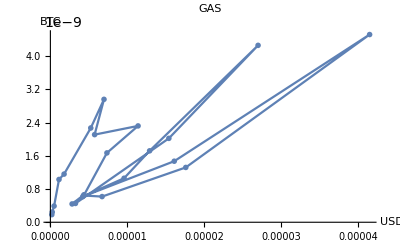

```mathematica
curr1=Import[NotebookDirectory[]<>"newdata.csv"];
curr2=Import[NotebookDirectory[]<>"newdata.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data = {curr1[[All,19]],curr2[[All,20]]}//Transpose;
labels = curr1[[All,1]];
ListPlot[data->data,Joined->True,LabelingFunction->Automatic,PlotRange->All, PlotMarkers->{●}, PlotLabel->"GAS", AxesLabel->{"USD","BTC"}]
```

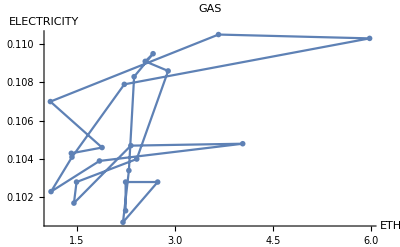

```mathematica
curr1=Import[NotebookDirectory[]<>"newdata.csv"];
curr2=Import[NotebookDirectory[]<>"newdata.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data = {curr1[[All,27]],curr2[[All,26]]}//Transpose;
labels = curr1[[All,1]];
ListPlot[data->data,Joined->True,LabelingFunction->Automatic,PlotRange->All, PlotMarkers->{●}, PlotLabel->"GAS", AxesLabel->{"ETH","ELECTRICITY"}]
```

```mathematica
curr1=Import[NotebookDirectory[]<>"newdata.csv"];
curr2=Import[NotebookDirectory[]<>"newdata.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data = {curr1[[All,9]],curr2[[All,29]]}//Transpose;
labels = curr1[[All,1]];
ListPlot[data->labels,Joined->True,LabelingFunction->Automatic,PlotRange->All, PlotMarkers->{●}, PlotLabel->"GBP", AxesLabel->{"USD","EUR"}]
```

-Graphics-

```mathematica
A=FinancialData["GBP/USD",{{2016,01,01},{2019,01,01},"Month"}]
B= FinancialData["GBP/EUR",{{2016,01,01},{2019,01,01},"Month"}]
{A[[All,1]],B[[All,1]]}//TableForm;
```

{{{2016,1,30},1.4246},{{2016,2,29},1.38617},{{2016,3,31},1.43725},{{2016,4,30},1.46155},{{2016,5,31},1.46325},{{2016,6,30},1.34525},{{2016,7,31},1.32315},{{2016,8,31},1.30906},{{2016,9,30},1.29648},{{2016,10,31},1.22063},{{2016,11,30},1.24907},{{2016,12,31},1.2342},{{2017,1,31},1.25007},{{2017,2,28},1.2438},{{2017,3,31},1.24773},{{2017,4,30},1.29385},{{2017,5,31},1.28087},{{2017,6,30},1.30086},{{2017,7,31},1.31435},{{2017,8,31},1.29195},{{2017,9,30},1.33985},{{2017,10,31},1.32136},{{2017,11,30},1.3417},{{2017,12,30},1.35113},{{2018,1,31},1.4156},{{2018,2,28},1.39047},{{2018,3,31},1.4015},{{2018,4,30},1.37691},{{2018,5,31},1.32843},{{2018,6,30},1.3205},{{2018,7,31},1.3136},{{2018,8,31},1.30113},{{2018,9,29},1.30294},{{2018,10,31},1.27075},{{2018,11,30},1.27854},{{2018,12,31},1.269},{{2019,1,1},1.2754}}

{{{2016,1,30},1.31467},{{2016,2,29},1.26892},{{2016,3,31},1.26815},{{2016,4,30},1.27624},{{2016,5,31},1.31267},{{2016,6,30},1.20971},{{2016,7,31},1.18385},{{2016,8,31},1.17412},{{2016,9,30},1.15564},{{2016,10,31},1.11146},{{2016,11,30},1.17312},{{2016,12,31},1.17231},{{2017,1,31},1.16743},{{2017,2,28},1.17512},{{2017,3,31},1.16742},{{2017,4,30},1.18751},{{2017,5,31},1.14645},{{2017,6,30},1.13718},{{2017,7,31},1.1189},{{2017,8,31},1.08656},{{2017,9,30},1.13406},{{2017,10,31},1.13411},{{2017,11,30},1.13193},{{2017,12,30},1.1267},{{2018,1,31},1.14076},{{2018,2,28},1.1373},{{2018,3,31},1.13729},{{2018,4,30},1.13591},{{2018,5,31},1.13885},{{2018,6,30},1.13009},{{2018,7,31},1.12201},{{2018,8,31},1.11536},{{2018,9,29},1.12286},{{2018,10,31},1.12005},{{2018,11,30},1.12224},{{2018,12,31},1.10934},{{2019,1,1},1.1082}}

```mathematica
curr1 =A;
curr2=B;
data = {curr1[[All,2]],curr2[[All,2]]}//Transpose;
labels = curr1[[All,1]];
ListPlot[data->labels,Joined->True,LabelingFunction->Automatic,PlotRange->All, PlotMarkers->{●}, PlotLabel->"GBP", AxesLabel->{"USD","EUR"},ImageSize-> 800]
```

-Graphics-

```mathematica
data1=FinancialData["EUR/USD",{{2016,01,01},{2019,01,01},"Month"}];
data2=FinancialData["CAD/USD",{{2016,01,01},{2019,01,01},"Month"}];
data3=FinancialData["GBP/USD",{{2016,01,01},{2019,01,01},"Month"}];
data4=FinancialData["BTC/USD",{{2016,01,01},{2019,01,01},"Month"}];
data4 =       data4[[All,2]]/1000
```

{0.37434,0.433835,0.414576,0.447582,0.513999,0.659749,0.620879,0.578944,0.60729,0.690001,0.735517,0.924678,0.959996,1.178,1.251,1.35999,2.43,2.54516,2.761,4.77,4.37155,6.40001,9.86789,13.5384,10.12,10.3211,7.,8.96459,7.49401,6.40363,7.71093,7.035,6.62117,6.30688,3.98871,3.69029,3.7968}

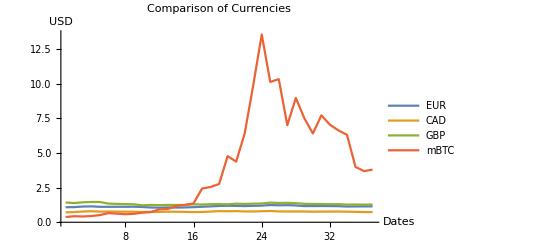

```mathematica
ListPlot[{data1[[All,2]],data2[[All,2]],data3[[All,2]],data4},Joined->True, PlotRange->All,PlotLegends-> {"EUR","CAD","GBP","mBTC" }, PlotLabel->"Comparison of Currencies", AxesLabel->{"Dates","USD"}]
```

```mathematica
data4=FinancialData["BTC/USD",{{2016,01,01},{2019,01,01}}];
  data4[[All,2]]= data4[[All,2]]/1000;
```

```mathematica
DateListPlot[{data1,data2,data3,data4},Joined->True, PlotRange->All,PlotLegends-> {"EUR","CAD","GBP","mBTC" }, PlotLabel->"Comparison of Currencies", AxesLabel->{"Dates","USD"},ImageSize->800,Filling->Axis]
```

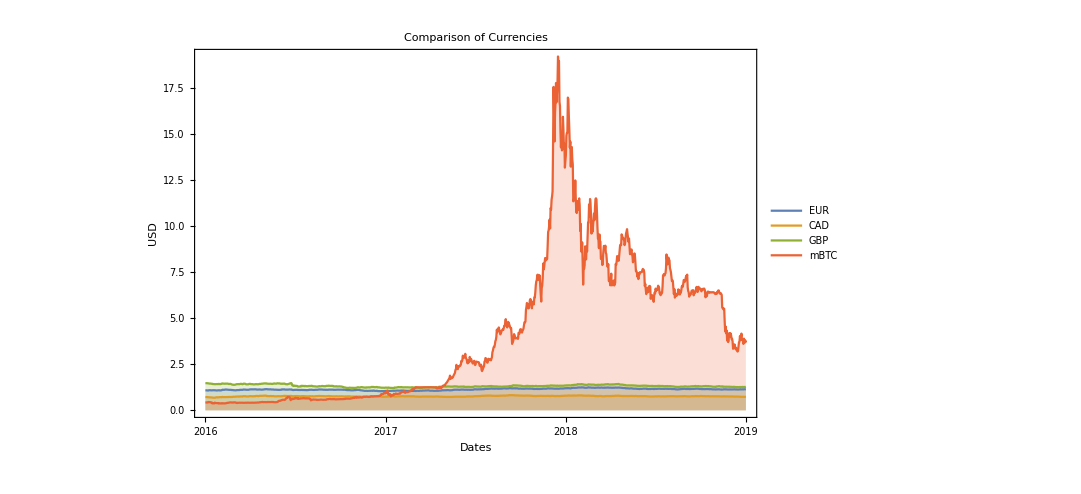

```mathematica
DateListPlot[{data1,data2,data3,data4},Joined->True, PlotRange->All,PlotLegends-> {"EUR","CAD","GBP","mBTC" }, PlotLabel->"Comparison of Currencies", AxesLabel->{"Dates","USD"},ImageSize->800,Filling->{4-> Axis}, PlotStyle->ColorData[16]]
```

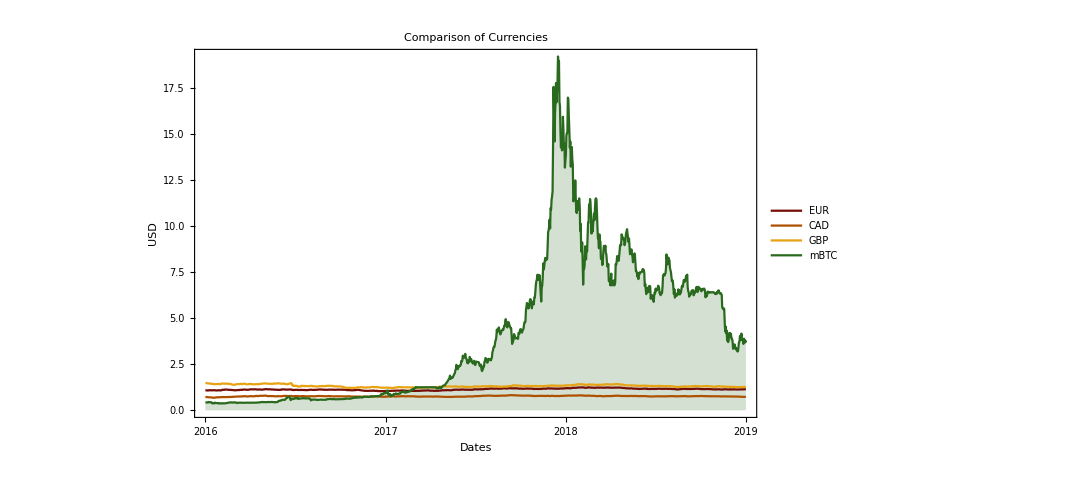

```mathematica
curr1=Import[NotebookDirectory[]<>"newdata.csv"];
curr2=Import[NotebookDirectory[]<>"newdata.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data = {curr1[[All,19]],curr2[[All,32]]}//Transpose;
labels = curr1[[All,1]];
ListPlot[data->labels,Joined->True,LabelingFunction->Automatic,PlotRange->All, PlotMarkers->{●}, PlotLabel->"GAS", AxesLabel->{"USD","ETH"},ImageSize->800]
```

-Graphics-

```mathematica
curr1=Import[NotebookDirectory[]<>"newdata.csv"];
curr2=Import[NotebookDirectory[]<>"newdata.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data = {curr1[[All,7]],curr2[[All,8]]}//Transpose;
labels = curr1[[All,1]];
ListPlot[data->labels,Joined->True,LabelingFunction->Automatic,  PlotRange->{{0.6,0.9} ,All},PlotMarkers->{●}, PlotLabel->"CAD", AxesLabel->{"USD","BTC"},ImageSize->400]
Export[NotebookDirectory[]<>"cad.pdf",%,"PDF"];

curr1=Import[NotebookDirectory[]<>"newdata.csv"];
curr2=Import[NotebookDirectory[]<>"newdata.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data = {curr1[[All,11]],curr2[[All,12]]}//Transpose;
labels = curr1[[All,1]];
ListPlot[data->labels,Joined->True,LabelingFunction->Automatic,PlotRange->{{1,1.3} ,All}, PlotMarkers->{●}, PlotLabel->"EUR", AxesLabel->{"USD","BTC"}, ImageSize->400]
Export[NotebookDirectory[]<>"eur.pdf",%,"PDF"];

curr1=Import[NotebookDirectory[]<>"newdata.csv"];
curr2=Import[NotebookDirectory[]<>"newdata.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data = {curr1[[All,21]],curr2[[All,22]]}//Transpose;
labels = curr1[[All,1]];
ListPlot[data->labels,Joined->True,LabelingFunction->Automatic,PlotRange->{{0.85,1.15} ,All}, PlotMarkers->{●}, PlotLabel->"TETHER", AxesLabel->{"USD","BTC"},
 ImageSize->400]
Export[NotebookDirectory[]<>"tether.pdf",%,"PDF"];

curr1=Import[NotebookDirectory[]<>"newdata.csv"];
curr2=Import[NotebookDirectory[]<>"newdata.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data = {curr1[[All,23]],curr2[[All,24]]}//Transpose;
labels = curr1[[All,1]];
ListPlot[data->labels,Joined->True,LabelingFunction->Automatic,PlotRange->{{0.85,1.15} ,All}, PlotMarkers->{●}, PlotLabel->"BitUSD", AxesLabel->{"USD","BTC"}, ImageSize->400]
Export[NotebookDirectory[]<>"bitusd.pdf",%,"PDF"];

curr1=Import[NotebookDirectory[]<>"newdata.csv"];
curr2=Import[NotebookDirectory[]<>"newdata.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data = {curr1[[All,19]],curr2[[All,20]]}//Transpose;
labels = curr1[[All,1]];
ListPlot[data->labels,Joined->True,LabelingFunction->Automatic,PlotRange->All, PlotMarkers->{●}, PlotLabel->"GAS", AxesLabel->{"USD","BTC"},ImageSize->400]
Export[NotebookDirectory[]<>"gas.pdf",%,"PDF"];

curr1=Import[NotebookDirectory[]<>"newdata.csv"];
curr2=Import[NotebookDirectory[]<>"newdata.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data = {curr1[[All,27]],curr2[[All,26]]}//Transpose;
labels = curr1[[All,1]];
ListPlot[data->labels,Joined->True,LabelingFunction->Automatic,PlotRange->All, PlotMarkers->{●}, PlotLabel->"GAS", AxesLabel->{"ETH","ELECTRICITY"},ImageSize->800]
Export[NotebookDirectory[]<>"gaselectricity.pdf",%,"PDF"];
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
a=-Graphics-
Export[NotebookDirectory[]<>"cad.pdf",a,"PDF"];
a=-Graphics-
Export[NotebookDirectory[]<>"eur.pdf",a,"PDF"];
a=-Graphics-
Export[NotebookDirectory[]<>"tether.pdf",a,"PDF"];
a=-Graphics-
Export[NotebookDirectory[]<>"bitusd.pdf",a,"PDF"];

a=-Graphics-
Export[NotebookDirectory[]<>"gas.pdf",a,"PDF"];
a=-Graphics-
Export[NotebookDirectory[]<>"gaselectricity.pdf",a,"PDF"];
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
a=-Graphics-
Export[NotebookDirectory[]<>"xrp.pdf",a,"PDF"];
```

-Graphics-

```mathematica
a=-Graphics-
Export[NotebookDirectory[]<>"eth.pdf",a,"PDF"];
```

-Graphics-

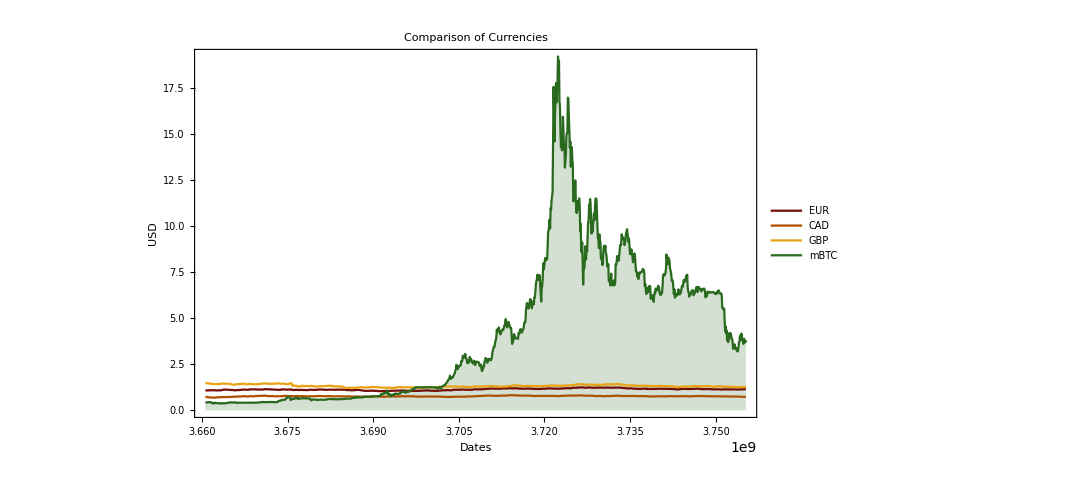

```mathematica
data1=FinancialData["EUR/USD",{{2016,01,01},{2019,01,01}}];
data2=FinancialData["CAD/USD",{{2016,01,01},{2019,01,01}}];
data3=FinancialData["GBP/USD",{{2016,01,01},{2019,01,01}}];
data4=FinancialData["BTC/USD",{{2016,01,01},{2019,01,01}}];
data4[[All,2]]= data4[[All,2]]/1000;
DateListPlot[{data1,data2,data3,data4},Joined->True, PlotRange->All,PlotLegends-> {"EUR","CAD","GBP","mBTC" }, PlotLabel->"Comparison of Currencies", ImageSize->800,Filling->{4-> Axis}, PlotStyle->ColorData[16], FrameLabel->{"Dates","USD"}]
Export[NotebookDirectory[]<>"allCurrencies.pdf",%,"PDF"];
```

```mathematica
curr1=Import[NotebookDirectory[]<>"newdata.csv"];
curr2=Import[NotebookDirectory[]<>"newdata.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data = {curr1[[All,19]],curr2[[All,27]]}//Transpose;
labels = curr1[[All,1]];
ListPlot[data->labels,Joined->True,LabelingFunction->Automatic,PlotRange->All, PlotMarkers->{●}, PlotLabel->"GAS", AxesLabel->{"USD","ETH"},ImageSize->800]
```

-Graphics-

```mathematica
-Graphics-

Export[NotebookDirectory[]<>"gas.pdf",%,"PDF"];
```

-Graphics-

```mathematica
curr1=Import[NotebookDirectory[]<>"newdata.csv"];
curr2=Import[NotebookDirectory[]<>"newdata.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data = {curr1[[All,30]],curr2[[All,27]]}//Transpose;
labels = curr1[[All,1]];
ListPlot[data->labels,Joined->True,LabelingFunction->Automatic,PlotRange->All, PlotMarkers->{●}, PlotLabel->"GAS", AxesLabel->{"ELECTRICITY","ETH"},ImageSize->800]
```

-Graphics-

```mathematica
-Graphics-
Export[NotebookDirectory[]<>"gaselectricity.pdf",%,"PDF"];
```

-Graphics-